```mathematica
(* The list of prime factors of n *)
PrimeFactors[n_Integer]:=Flatten[Take[Transpose[FactorInteger[n]],1]];

(* The index [\Gamma:\Gamma_0(n)];*)
GG0Index[n_Integer]:=
Module[{l,s,i},
l=PrimeFactors[n];
s=n;
For[i=1,i<=Length[l],i++,
s*=1+1/l[[i]];
];
Return[s];
];
(* The number of order-2 and order-3 cone points;*)
(*Note that the number of ideal triangles in a $\Gamma_0(n)$--special triangle is (GG0Index[n]-v3[n])/3;*)
(*  which is also an upperbound for the iterates *)
v2[n_Integer]:=
Module[{l,s,i,r},
If[Mod[n,4]==0,Return[0]];
l=PrimeFactors[n];
s=1;

For[i=1,i<=Length[l],i++,

r=Mod[l[[i]],4];

If[r==3,Return[0],If[r==1,s*=2]];
];
Return[s];
];
v3[n_Integer]:=
Module[{l,s,i,r},
If[Mod[n,9]==0,Return[0]];
l=PrimeFactors[n];
s=1;

For[i=1,i<=Length[l],i++,

r=Mod[l[[i]],3];

If[r==2,Return[0],If[r==1,s*=2]];
];
Return[s];
];
(* Totient summatory function *)
Summatory[m_Integer]:=Sum[EulerPhi[i],{i,1,m}];
SqStartSpPoly[n_Integer]:=
Module[{t,iterateMax,iterate,vw,vb,k,Found,unclaimed,mpos,m,j,j1,res,m1,cpt=False,v2count=0,v3count=0,v2value,v3value},
iterateMax=(GG0Index[n]-v3[n])/3;
t=Floor[Sqrt[n]];

v2value=v2[n];
v3value=v3[n];

vw=Denominator[FareySequence[t]];
vb=Table[-4,Length[vw]-1];


k=0;
Found=False;
For[iterate=1,iterate<=iterateMax&&!Found,iterate++,
For[j=1,j<Length[vw],j++,
If[vb[[j]]!=-4,Continue[]];
(* Check if even *)
If[v2count<v2value,
If[Mod[vw[[j]]^2+vw[[j+1]]^2,n]==0,vb=ReplacePart[vb,j->-2];v2count++;Continue[]]];
(* Check if odd *)
If[v3count<v3value,
If[Mod[vw[[j]]^2+vw[[j]]vw[[j+1]]+vw[[j+1]]^2,n]==0,vb=ReplacePart[vb,j->-3];v3count++;Continue[]]];
For[j1=j+1,j1<Length[vw],j1++,
If[vb[[j1]]==-4&&Mod[vw[[j]]vw[[j1]]+vw[[j+1]]vw[[j1+1]],n]==0,vb=ReplacePart[vb,j->++k];
vb=ReplacePart[vb,j1->k];Continue[]]];
];

unclaimed=Flatten[Position[vb,-4]];
(* If no black vertices are labeled -4, then our computation is complete and safe *)

If[unclaimed=={},
Found=True;res=Max[vw];
Break[]
];

mpos=1;
m=Plus[vw[[unclaimed[[1]]]],vw[[unclaimed[[1]]+1]]];
For[j=2,j<=Length[unclaimed],j++,
m1=Plus[vw[[unclaimed[[j]]]],vw[[unclaimed[[j]]+1]]];
If[m>m1,mpos=j;m=m1;
];
];
j=unclaimed[[mpos]];
vw = Insert[vw,vw[[j]]+vw[[j+1]],j+1];
vb=Insert[vb,-4,j+1];
];
Return[{vw,vb}];
];

(* Starting from zero assumptions on the denominators,
find gFS by choosing the smallest denominator sums at each moment,
and outputs (denominators, labels, maximum 2,1 component needed ) *)
ZeroStartSpPoly[n_Integer]:=
Module[{maxmulti=0,t,iterateMax,iterate,vw,vb,k,Found,unclaimed,mpos,m,j,j1,res,m1,cpt=False,v2count=0,v3count=0,v2value,v3value,temp},
iterateMax=(GG0Index[n]-v3[n])/3;
t=1;

v2value=v2[n];
v3value=v3[n];

vw=Denominator[FareySequence[t]];
vb=Table[-4,Length[vw]-1];


k=0;
Found=False;
For[iterate=1,iterate<=iterateMax&&!Found,iterate++,
For[j=1,j<Length[vw],j++,
If[vb[[j]]!=-4,Continue[]];
(* Check if even *)
If[v2count<v2value,
temp=vw[[j]]^2+vw[[j+1]]^2;
If[Mod[temp,n]==0,
maxmulti=Max[maxmulti,temp];
vb=ReplacePart[vb,j->-2];v2count++;Continue[]
]
];
(* Check if odd *)
If[v3count<v3value,
temp=vw[[j]]^2+vw[[j]]vw[[j+1]]+vw[[j+1]]^2;
If[Mod[temp,n]==0,maxmulti=Max[maxmulti,temp];vb=ReplacePart[vb,j->-3];v3count++;Continue[]]];


For[j1=j+1,j1<Length[vw],j1++,
temp=vw[[j]]vw[[j1]]+vw[[j+1]]vw[[j1+1]];
If[vb[[j1]]==-4&&Mod[temp,n]==0,maxmulti=Max[maxmulti,temp];vb=ReplacePart[vb,j->++k];
vb=ReplacePart[vb,j1->k];Continue[]]];
];

unclaimed=Flatten[Position[vb,-4]];
(* If no black vertices are labeled -4, then our computation is complete and safe *)

If[unclaimed=={},
Found=True;res=Max[vw];
Break[]
];

mpos=1;
m=Plus[vw[[unclaimed[[1]]]],vw[[unclaimed[[1]]+1]]];
For[j=2,j<=Length[unclaimed],j++,
m1=Plus[vw[[unclaimed[[j]]]],vw[[unclaimed[[j]]+1]]];
If[m>m1,mpos=j;m=m1;
];
];
j=unclaimed[[mpos]];
vw = Insert[vw,vw[[j]]+vw[[j+1]],j+1];
vb=Insert[vb,-4,j+1];
];
Return[{vw,vb,maxmulti}];
];
PrintSpPoly[n_Integer]:=
Module[{t,iterateMax,iterate,vw,vb,k,Found,unclaimed,mpos,m,j,j1,res,m1,cpt=False,v2count=0,v3count=0,v2value,v3value},
iterateMax=(GG0Index[n]-v3[n])/3;
t=Floor[Sqrt[n]];

v2value=v2[n];
v3value=v3[n];

vw=Denominator[FareySequence[t]];
vb=Table[-4,Length[vw]-1];


k=0;
Found=False;
For[iterate=1,iterate<=iterateMax&&!Found,iterate++,
For[j=1,j<Length[vw],j++,
If[vb[[j]]!=-4,Continue[]];
(* Check if even *)
If[v2count<v2value,
If[Mod[vw[[j]]^2+vw[[j+1]]^2,n]==0,vb=ReplacePart[vb,j->-2];v2count++;Continue[]]];
(* Check if odd *)
If[v3count<v3value,
If[Mod[vw[[j]]^2+vw[[j]]vw[[j+1]]+vw[[j+1]]^2,n]==0,vb=ReplacePart[vb,j->-3];v3count++;Continue[]]];
For[j1=j+1,j1<Length[vw],j1++,
If[vb[[j1]]==-4&&Mod[vw[[j]]vw[[j1]]+vw[[j+1]]vw[[j1+1]],n]==0,vb=ReplacePart[vb,j->++k];
vb=ReplacePart[vb,j1->k];Continue[]]];
];

unclaimed=Flatten[Position[vb,-4]];
(* If no black vertices are labeled -4, then our computation is complete and safe *)

If[unclaimed=={},
Found=True;res=Max[vw];
Break[]
];

mpos=1;
m=Plus[vw[[unclaimed[[1]]]],vw[[unclaimed[[1]]+1]]];
For[j=2,j<=Length[unclaimed],j++,
m1=Plus[vw[[unclaimed[[j]]]],vw[[unclaimed[[j]]+1]]];
If[m>m1,mpos=j;m=m1;
];
];
j=unclaimed[[mpos]];
vw = Insert[vw,vw[[j]]+vw[[j+1]],j+1];
vb=Insert[vb,-4,j+1];
Print[vw];
Print[vb];
];
Return[{vw,vb}];
];
```

```mathematica
CashewList[aMax_Integer]:=
Module[{a,s,b,t,MM,l={}},
For[a=1,a<=aMax,a++,
For[s=1,s<=a-1,s++,
For[t=a-s+1,t<=a-1,t++,
For[b=a-s,b<=t,b++,
MM=a s + b t;
If[IntegerQ[Sqrt[4MM/3]]&&!MemberQ[l,MM],AppendTo[l,MM]];
]]]];
Return[l]];
```

```mathematica
CashewList[5000]
```

$Aborted

```mathematica
SqMaxSpPoly[n_Integer]:=
Module[{t,iterateMax,iterate,vw,vb,k,Found,unclaimed,mpos,m,j,j1,res,m1,cpt=False,v2count=0,v3count=0,v2value,v3value},
iterateMax=(GG0Index[n]-v3[n])/3;
t=Floor[Sqrt[n]];

v2value=v2[n];
v3value=v3[n];

vw=Denominator[FareySequence[t]];
vb=Table[-4,Length[vw]-1];


k=0;
Found=False;
For[iterate=1,iterate<=iterateMax&&!Found,iterate++,
For[j=1,j<Length[vw],j++,
If[vb[[j]]!=-4,Continue[]];
(* Check if even *)
If[v2count<v2value,
If[Mod[vw[[j]]^2+vw[[j+1]]^2,n]==0,vb=ReplacePart[vb,j->-2];v2count++;Continue[]]];
(* Check if odd *)
If[v3count<v3value,
If[Mod[vw[[j]]^2+vw[[j]]vw[[j+1]]+vw[[j+1]]^2,n]==0,vb=ReplacePart[vb,j->-3];v3count++;Continue[]]];
For[j1=j+1,j1<Length[vw],j1++,
If[vb[[j1]]==-4&&Mod[vw[[j]]vw[[j1]]+vw[[j+1]]vw[[j1+1]],n]==0,vb=ReplacePart[vb,j->++k];
vb=ReplacePart[vb,j1->k];Continue[]]];
];

unclaimed=Flatten[Position[vb,-4]];
(* If no black vertices are labeled -4, then our computation is complete and safe *)

If[unclaimed=={},
Found=True;res=Max[vw];
Break[]
];

mpos=1;
m=Plus[vw[[unclaimed[[1]]]],vw[[unclaimed[[1]]+1]]];
For[j=2,j<=Length[unclaimed],j++,
m1=Plus[vw[[unclaimed[[j]]]],vw[[unclaimed[[j]]+1]]];
If[m<m1,mpos=j;m=m1;
];
];
j=unclaimed[[mpos]];
vw = Insert[vw,vw[[j]]+vw[[j+1]],j+1];
vb=Insert[vb,-4,j+1];
];
Return[{vw,vb}];
];
```

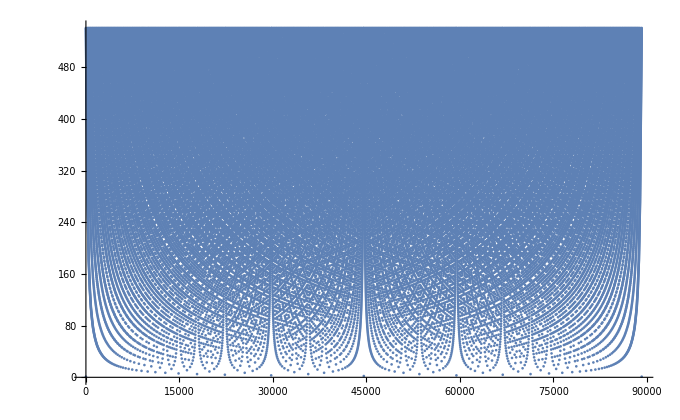

```mathematica
ListPlot[Denominator[FareySequence[p]]]
```

```mathematica
ZeroStartSpPoly[43*47]
```

{{1,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,49,24,47,23,45,22,43,21,41,20,39,19,37,18,35,17,33,49,16,47,31,46,15,44,29,43,14,41,27,40,13,38,25,37,12,47,35,23,34,45,11,43,32,21,31,41,10,49,39,29,48,19,47,28,37,46,9,44,35,26,43,17,42,25,33,41,8,47,39,31,23,38,15,37,22,51,29,36,43,7,41,34,27,47,20,33,46,13,45,32,19,44,25,31,37,43,6,47,41,35,29,23,40,17,45,28,39,11,38,27,43,16,37,21,47,26,31,36,41,46,5,44,39,34,29,24,43,19,33,47,14,37,23,32,41,9,40,31,22,35,13,43,30,47,17,38,21,46,25,29,33,37,41,4,47,43,39,35,31,27,50,23,42,19,34,15,41,26,37,11,40,29,47,18,43,25,32,39,7,45,38,31,24,41,17,44,27,37,47,10,43,33,23,36,49,13,42,29,45,16,35,19,41,22,47,25,28,31,34,37,40,43,3,47,44,41,38,35,32,29,26,23,43,20,37,17,31,45,14,39,25,36,47,11,41,30,49,19,27,35,43,8,45,37,29,21,34,47,13,44,31,49,18,41,23,28,33,38,43,5,47,42,37,32,27,22,39,17,46,29,41,12,43,31,19,45,26,33,40,47,7,44,37,30,23,39,16,41,25,34,43,9,47,38,29,49,20,31,42,11,46,35,24,37,13,41,28,43,15,47,32,49,17,36,19,40,21,44,23,48,25,27,29,31,33,35,37,39,41,43,45,47,2,43,41,39,37,35,33,31,29,27,25,48,23,44,21,40,19,36,17,49,32,47,15,43,28,41,13,37,24,35,46,11,42,31,51,20,29,38,47,9,43,34,25,41,16,39,23,30,37,44,7,47,40,33,26,45,19,31,43,12,41,29,46,17,39,22,27,32,37,42,47,5,43,38,33,28,23,41,18,49,31,44,13,47,34,21,29,37,45,8,43,35,27,46,19,30,41,11,47,36,25,39,14,45,31,17,37,20,43,23,26,29,32,35,38,41,44,47,3,43,40,37,34,31,28,25,47,22,41,19,35,16,45,29,42,13,49,36,23,33,43,10,47,37,27,44,17,41,24,31,38,45,7,39,32,25,43,18,47,29,40,11,37,26,41,15,34,19,42,23,50,27,31,35,39,43,47,4,45,41,37,33,29,25,46,21,38,17,47,30,43,13,35,22,31,40,9,41,32,23,37,14,47,33,19,43,24,29,34,39,44,5,41,36,31,26,47,21,37,16,43,27,38,49,11,39,28,45,17,40,23,29,35,41,47,6,43,37,31,25,44,19,32,45,13,46,33,20,47,27,34,41,7,43,36,29,22,37,15,38,23,31,39,47,8,41,33,25,42,17,43,26,35,44,9,46,37,28,47,19,48,29,39,10,41,31,21,32,43,11,45,34,23,35,47,12,37,25,38,13,40,27,41,14,43,29,44,15,46,31,47,16,49,33,17,35,18,37,19,39,20,41,21,43,22,45,23,47,24,49,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,1},{197,198,165,138,107,67,55,226,23,103,5,166,94,22,18,84,325,28,345,222,260,317,318,302,299,199,200,128,127,68,77,48,211,264,85,333,327,337,319,320,300,266,238,239,166,167,145,143,69,244,56,230,246,124,11,126,266,267,65,224,201,202,155,134,328,334,177,71,321,322,37,309,310,307,274,82,240,241,168,169,6,127,147,108,109,17,70,200,267,268,38,36,24,75,80,12,349,350,7,158,129,185,71,25,305,308,63,242,243,203,204,55,170,171,92,13,144,133,288,275,72,110,201,57,232,205,206,39,339,322,25,130,136,338,95,286,291,5,6,73,245,244,173,172,40,1,343,142,132,311,270,269,73,33,32,74,239,194,115,351,14,178,135,157,271,295,125,243,246,247,344,2,14,75,198,268,290,140,41,248,218,346,345,111,110,70,169,262,76,236,249,116,192,269,287,160,128,206,61,207,208,207,26,49,78,77,173,174,15,297,270,153,161,310,170,323,324,112,113,209,210,87,113,79,220,296,289,204,53,2,47,58,129,165,278,279,228,80,27,24,96,98,213,149,130,62,40,252,212,211,215,54,7,272,276,225,81,326,325,245,57,137,146,214,213,253,106,190,277,271,175,176,328,327,82,120,346,29,28,131,164,273,284,114,16,20,188,174,42,248,249,83,119,141,151,240,215,216,247,59,285,272,177,178,43,45,43,100,234,84,179,148,131,281,273,29,329,330,349,116,115,250,251,52,68,320,111,85,132,159,274,282,331,332,341,180,60,83,179,180,311,312,309,312,39,4,21,186,44,86,133,217,275,298,217,154,87,45,175,12,1,51,313,315,313,314,181,182,90,61,181,319,333,334,276,303,134,150,88,122,342,104,38,252,253,117,118,352,351,326,30,280,277,139,135,182,89,202,72,46,44,46,183,184,283,278,62,258,218,219,263,136,137,114,90,254,255,47,187,172,13,17,119,279,280,138,139,31,30,347,112,91,335,336,185,186,292,281,171,67,250,221,220,140,141,64,256,257,329,92,210,282,283,9,48,219,223,222,251,50,59,152,142,221,74,76,35,32,93,197,284,285,196,156,63,42,3,37,233,287,286,214,94,121,86,225,224,121,120,338,337,191,316,143,144,293,288,18,187,189,105,95,41,33,227,226,227,60,231,162,145,289,294,168,118,254,199,96,241,193,101,123,122,348,347,216,255,49,146,290,301,228,229,97,19,3,318,258,259,261,109,291,292,147,148,183,19,350,117,167,265,98,27,26,99,294,293,314,150,149,317,4,50,188,189,256,99,8,10,295,296,78,324,151,152,34,339,340,321,51,231,230,203,64,235,123,100,298,297,154,153,20,81,190,191,66,233,232,261,260,58,299,300,34,102,176,156,155,9,352,21,93,97,35,23,52,301,304,237,101,16,125,124,157,163,8,193,192,262,263,91,303,302,316,315,53,340,102,184,331,336,159,158,234,235,209,56,304,306,107,22,108,259,205,65,257,103,161,160,194,195,265,264,306,305,342,341,323,335,332,88,238,223,54,105,104,163,162,237,236,308,307,344,343,242,212,348,31,330,89,15,11,79,195,10,69,36,208,66,106,126,164,196,229},4042}

```mathematica
l={{1,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,49,24,47,23,45,22,43,21,41,20,39,19,37,18,35,17,33,49,16,47,31,46,15,44,29,43,14,41,27,40,13,38,25,37,12,47,35,23,34,45,11,43,32,21,31,41,10,49,39,29,48,19,47,28,37,46,9,44,35,26,43,17,42,25,33,41,8,47,39,31,23,38,15,37,22,51,29,36,43,7,41,34,27,47,20,33,46,13,45,32,19,44,25,31,37,43,6,47,41,35,29,23,40,17,45,28,39,11,38,27,43,16,37,21,47,26,31,36,41,46,5,44,39,34,29,24,43,19,33,47,14,37,23,32,41,9,40,31,22,35,13,43,30,47,17,38,21,46,25,29,33,37,41,4,47,43,39,35,31,27,50,23,42,19,34,15,41,26,37,11,40,29,47,18,43,25,32,39,7,45,38,31,24,41,17,44,27,37,47,10,43,33,23,36,49,13,42,29,45,16,35,19,41,22,47,25,28,31,34,37,40,43,3,47,44,41,38,35,32,29,26,23,43,20,37,17,31,45,14,39,25,36,47,11,41,30,49,19,27,35,43,8,45,37,29,21,34,47,13,44,31,49,18,41,23,28,33,38,43,5,47,42,37,32,27,22,39,17,46,29,41,12,43,31,19,45,26,33,40,47,7,44,37,30,23,39,16,41,25,34,43,9,47,38,29,49,20,31,42,11,46,35,24,37,13,41,28,43,15,47,32,49,17,36,19,40,21,44,23,48,25,27,29,31,33,35,37,39,41,43,45,47,2,43,41,39,37,35,33,31,29,27,25,48,23,44,21,40,19,36,17,49,32,47,15,43,28,41,13,37,24,35,46,11,42,31,51,20,29,38,47,9,43,34,25,41,16,39,23,30,37,44,7,47,40,33,26,45,19,31,43,12,41,29,46,17,39,22,27,32,37,42,47,5,43,38,33,28,23,41,18,49,31,44,13,47,34,21,29,37,45,8,43,35,27,46,19,30,41,11,47,36,25,39,14,45,31,17,37,20,43,23,26,29,32,35,38,41,44,47,3,43,40,37,34,31,28,25,47,22,41,19,35,16,45,29,42,13,49,36,23,33,43,10,47,37,27,44,17,41,24,31,38,45,7,39,32,25,43,18,47,29,40,11,37,26,41,15,34,19,42,23,50,27,31,35,39,43,47,4,45,41,37,33,29,25,46,21,38,17,47,30,43,13,35,22,31,40,9,41,32,23,37,14,47,33,19,43,24,29,34,39,44,5,41,36,31,26,47,21,37,16,43,27,38,49,11,39,28,45,17,40,23,29,35,41,47,6,43,37,31,25,44,19,32,45,13,46,33,20,47,27,34,41,7,43,36,29,22,37,15,38,23,31,39,47,8,41,33,25,42,17,43,26,35,44,9,46,37,28,47,19,48,29,39,10,41,31,21,32,43,11,45,34,23,35,47,12,37,25,38,13,40,27,41,14,43,29,44,15,46,31,47,16,49,33,17,35,18,37,19,39,20,41,21,43,22,45,23,47,24,49,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,1},{197,198,1,2,3,4,5,226,6,7,8,9,10,11,12,13,325,14,345,222,260,317,318,302,299,199,200,15,16,17,18,19,211,264,20,333,327,337,319,320,300,266,238,239,9,21,22,23,24,244,25,230,246,26,27,28,266,267,29,224,201,202,30,31,328,334,32,33,321,322,34,309,310,307,274,35,240,241,36,37,38,16,39,40,41,42,43,200,267,268,44,45,46,47,48,49,349,350,50,51,52,53,33,54,305,308,55,242,243,203,204,5,56,57,58,59,60,61,288,275,62,63,201,64,232,205,206,65,339,322,54,66,67,338,68,286,291,8,38,69,245,244,70,71,72,73,343,74,75,311,270,269,69,76,77,78,239,79,80,351,81,82,83,84,271,295,85,243,246,247,344,86,81,47,198,268,290,87,88,248,218,346,345,89,63,43,37,262,90,236,249,91,92,269,287,93,15,206,94,207,208,207,95,96,97,18,70,98,99,297,270,100,101,310,56,323,324,102,103,209,210,104,103,105,220,296,289,204,106,86,107,108,52,1,278,279,228,48,109,46,110,111,213,112,66,113,72,252,212,211,215,114,50,272,276,225,115,326,325,245,64,116,117,214,213,253,118,119,277,271,120,121,328,327,35,122,346,123,14,124,125,273,284,126,127,128,129,98,130,248,249,131,132,133,134,240,215,216,247,135,285,272,32,82,136,137,136,138,234,13,139,140,124,281,273,123,329,330,349,91,80,250,251,141,17,320,89,20,75,142,274,282,331,332,341,143,144,131,139,143,311,312,309,312,65,145,146,147,148,149,61,217,275,298,217,150,104,137,120,49,73,151,313,315,313,314,152,153,154,94,152,319,333,334,276,303,31,155,156,157,342,158,44,252,253,159,160,352,351,326,161,280,277,162,83,153,163,202,62,164,148,164,165,166,283,278,113,258,218,219,263,67,116,126,154,254,255,107,167,71,59,42,132,279,280,2,162,168,161,347,102,169,335,336,53,147,292,281,57,4,250,221,220,87,133,170,256,257,329,58,210,282,283,171,19,219,223,222,251,172,135,173,74,221,78,90,174,77,175,197,284,285,176,177,55,130,178,34,233,287,286,214,10,179,149,225,224,179,122,338,337,180,316,23,60,293,288,12,167,181,182,68,88,76,227,226,227,144,231,183,22,289,294,36,160,254,199,110,241,184,185,186,157,348,347,216,255,96,117,290,301,228,229,187,188,178,318,258,259,261,41,291,292,39,140,165,188,350,159,21,265,111,109,95,189,294,293,314,155,112,317,145,172,129,181,256,189,190,191,295,296,97,324,134,173,192,339,340,321,151,231,230,203,170,235,186,138,298,297,150,100,128,115,119,180,193,233,232,261,260,108,299,300,192,194,121,177,30,171,352,146,175,187,174,6,141,301,304,237,185,127,85,26,84,195,190,184,92,262,263,169,303,302,316,315,106,340,194,166,331,336,142,51,234,235,209,25,304,306,3,11,40,259,205,29,257,7,101,93,79,196,265,264,306,305,342,341,323,335,332,156,238,223,114,182,158,195,183,237,236,308,307,344,343,242,212,348,168,330,163,99,27,105,196,191,24,45,208,193,118,28,125,176,229}};
```

```mathematica
l[[3]]
```

Part::partw: Part 3 of {{1,45,44,43,42,41,40,39,38,37,«695»},{197,198,1,2,3,4,5,226,6,7,«694»}} does not exist.

{{1,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,49,24,47,23,45,22,43,21,41,20,39,19,37,18,35,17,33,49,16,47,31,46,15,44,29,43,14,41,27,40,13,38,25,37,12,47,35,23,34,45,11,43,32,21,31,41,10,49,39,29,48,19,47,28,37,46,9,44,35,26,43,17,42,25,33,41,8,47,39,31,23,38,15,37,22,51,29,36,43,7,41,34,27,47,20,33,46,13,45,32,19,44,25,31,37,43,6,47,41,35,29,23,40,17,45,28,39,11,38,27,43,16,37,21,47,26,31,36,41,46,5,44,39,34,29,24,43,19,33,47,14,37,23,32,41,9,40,31,22,35,13,43,30,47,17,38,21,46,25,29,33,37,41,4,47,43,39,35,31,27,50,23,42,19,34,15,41,26,37,11,40,29,47,18,43,25,32,39,7,45,38,31,24,41,17,44,27,37,47,10,43,33,23,36,49,13,42,29,45,16,35,19,41,22,47,25,28,31,34,37,40,43,3,47,44,41,38,35,32,29,26,23,43,20,37,17,31,45,14,39,25,36,47,11,41,30,49,19,27,35,43,8,45,37,29,21,34,47,13,44,31,49,18,41,23,28,33,38,43,5,47,42,37,32,27,22,39,17,46,29,41,12,43,31,19,45,26,33,40,47,7,44,37,30,23,39,16,41,25,34,43,9,47,38,29,49,20,31,42,11,46,35,24,37,13,41,28,43,15,47,32,49,17,36,19,40,21,44,23,48,25,27,29,31,33,35,37,39,41,43,45,47,2,43,41,39,37,35,33,31,29,27,25,48,23,44,21,40,19,36,17,49,32,47,15,43,28,41,13,37,24,35,46,11,42,31,51,20,29,38,47,9,43,34,25,41,16,39,23,30,37,44,7,47,40,33,26,45,19,31,43,12,41,29,46,17,39,22,27,32,37,42,47,5,43,38,33,28,23,41,18,49,31,44,13,47,34,21,29,37,45,8,43,35,27,46,19,30,41,11,47,36,25,39,14,45,31,17,37,20,43,23,26,29,32,35,38,41,44,47,3,43,40,37,34,31,28,25,47,22,41,19,35,16,45,29,42,13,49,36,23,33,43,10,47,37,27,44,17,41,24,31,38,45,7,39,32,25,43,18,47,29,40,11,37,26,41,15,34,19,42,23,50,27,31,35,39,43,47,4,45,41,37,33,29,25,46,21,38,17,47,30,43,13,35,22,31,40,9,41,32,23,37,14,47,33,19,43,24,29,34,39,44,5,41,36,31,26,47,21,37,16,43,27,38,49,11,39,28,45,17,40,23,29,35,41,47,6,43,37,31,25,44,19,32,45,13,46,33,20,47,27,34,41,7,43,36,29,22,37,15,38,23,31,39,47,8,41,33,25,42,17,43,26,35,44,9,46,37,28,47,19,48,29,39,10,41,31,21,32,43,11,45,34,23,35,47,12,37,25,38,13,40,27,41,14,43,29,44,15,46,31,47,16,49,33,17,35,18,37,19,39,20,41,21,43,22,45,23,47,24,49,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,1},{197,198,1,2,3,4,5,226,6,7,8,9,10,11,12,13,325,14,345,222,260,317,318,302,299,199,200,15,16,17,18,19,211,264,20,333,327,337,319,320,300,266,238,239,9,21,22,23,24,244,25,230,246,26,27,28,266,267,29,224,201,202,30,31,328,334,32,33,321,322,34,309,310,307,274,35,240,241,36,37,38,16,39,40,41,42,43,200,267,268,44,45,46,47,48,49,349,350,50,51,52,53,33,54,305,308,55,242,243,203,204,5,56,57,58,59,60,61,288,275,62,63,201,64,232,205,206,65,339,322,54,66,67,338,68,286,291,8,38,69,245,244,70,71,72,73,343,74,75,311,270,269,69,76,77,78,239,79,80,351,81,82,83,84,271,295,85,243,246,247,344,86,81,47,198,268,290,87,88,248,218,346,345,89,63,43,37,262,90,236,249,91,92,269,287,93,15,206,94,207,208,207,95,96,97,18,70,98,99,297,270,100,101,310,56,323,324,102,103,209,210,104,103,105,220,296,289,204,106,86,107,108,52,1,278,279,228,48,109,46,110,111,213,112,66,113,72,252,212,211,215,114,50,272,276,225,115,326,325,245,64,116,117,214,213,253,118,119,277,271,120,121,328,327,35,122,346,123,14,124,125,273,284,126,127,128,129,98,130,248,249,131,132,133,134,240,215,216,247,135,285,272,32,82,136,137,136,138,234,13,139,140,124,281,273,123,329,330,349,91,80,250,251,141,17,320,89,20,75,142,274,282,331,332,341,143,144,131,139,143,311,312,309,312,65,145,146,147,148,149,61,217,275,298,217,150,104,137,120,49,73,151,313,315,313,314,152,153,154,94,152,319,333,334,276,303,31,155,156,157,342,158,44,252,253,159,160,352,351,326,161,280,277,162,83,153,163,202,62,164,148,164,165,166,283,278,113,258,218,219,263,67,116,126,154,254,255,107,167,71,59,42,132,279,280,2,162,168,161,347,102,169,335,336,53,147,292,281,57,4,250,221,220,87,133,170,256,257,329,58,210,282,283,171,19,219,223,222,251,172,135,173,74,221,78,90,174,77,175,197,284,285,176,177,55,130,178,34,233,287,286,214,10,179,149,225,224,179,122,338,337,180,316,23,60,293,288,12,167,181,182,68,88,76,227,226,227,144,231,183,22,289,294,36,160,254,199,110,241,184,185,186,157,348,347,216,255,96,117,290,301,228,229,187,188,178,318,258,259,261,41,291,292,39,140,165,188,350,159,21,265,111,109,95,189,294,293,314,155,112,317,145,172,129,181,256,189,190,191,295,296,97,324,134,173,192,339,340,321,151,231,230,203,170,235,186,138,298,297,150,100,128,115,119,180,193,233,232,261,260,108,299,300,192,194,121,177,30,171,352,146,175,187,174,6,141,301,304,237,185,127,85,26,84,195,190,184,92,262,263,169,303,302,316,315,106,340,194,166,331,336,142,51,234,235,209,25,304,306,3,11,40,259,205,29,257,7,101,93,79,196,265,264,306,305,342,341,323,335,332,156,238,223,114,182,158,195,183,237,236,308,307,344,343,242,212,348,168,330,163,99,27,105,196,191,24,45,208,193,118,28,125,176,229}}⟦3⟧

```mathematica
p=11;
For[i=1,i<=5,i++,
Print["p = ",p," and i = ",i," and then p^i case max denom = ",Max[l=SqStartSpPoly[p^i][[1]]]]];
```

p = 11 and i = 1 and then p^i case max denom = 3

p = 11 and i = 2 and then p^i case max denom = 12

p = 11 and i = 3 and then p^i case max denom = 121

p = 11 and i = 4 and then p^i case max denom = 1331

$Aborted

```mathematica
p=11;
For[i=1,i<=3,i++,
Print["p = ",p," and i = ",i," and then p^i case max denom = ",Max[l=SqStartSpPoly[p^i][[1]]]]];
```

p = 11 and i = 1 and then p^i case max denom = 3

p = 11 and i = 2 and then p^i case max denom = 12

p = 11 and i = 3 and then p^i case max denom = 121

```mathematica
i=3;l2=SqStartSpPoly[p^i];
```

```mathematica
l2[[2]]
```

{1,2,3,4,5,6,222,7,8,9,10,11,12,135,13,14,15,187,188,115,116,144,221,233,233,223,16,17,18,19,20,21,191,192,182,155,117,118,156,22,20,23,24,148,25,122,187,183,26,217,119,160,27,132,195,24,28,162,151,139,120,121,16,29,30,31,32,223,213,33,34,35,219,234,234,225,36,37,122,123,166,38,39,40,41,128,173,174,197,124,125,37,42,43,30,3,220,44,199,45,46,126,127,168,32,175,46,47,9,153,142,175,176,48,163,14,128,129,170,49,50,51,193,208,39,49,130,131,4,52,201,205,125,207,227,177,52,193,194,158,132,226,214,159,53,54,216,55,50,212,12,5,56,57,204,15,133,134,171,58,59,60,210,146,135,136,178,231,235,235,208,152,61,34,62,63,42,64,232,205,137,138,217,236,236,227,65,117,174,44,195,196,66,67,121,203,230,139,68,69,70,211,237,237,229,43,71,10,72,73,185,140,141,124,141,192,31,68,178,179,189,74,75,76,77,143,142,64,59,8,78,26,79,179,80,214,66,18,81,62,82,116,144,145,70,83,35,84,85,215,61,180,41,86,22,87,88,89,147,146,36,17,67,65,188,180,181,90,91,197,198,149,164,149,148,173,13,7,92,29,93,230,238,238,212,82,33,90,150,229,204,169,75,85,199,200,94,186,172,74,228,239,239,218,152,151,206,231,89,95,60,83,96,80,138,209,240,240,232,181,153,154,143,207,63,88,40,118,156,155,97,203,51,53,98,99,211,100,6,213,48,56,131,215,225,157,130,201,202,101,182,228,210,165,206,194,101,102,159,158,103,104,209,202,57,100,103,119,160,161,105,126,54,183,184,147,136,106,28,107,184,108,120,162,163,107,23,196,94,219,109,110,93,95,111,165,164,191,186,185,161,79,58,104,21,123,166,167,111,77,226,241,241,220,81,96,69,216,224,108,91,110,71,112,169,168,150,137,127,47,113,200,157,19,129,170,218,86,176,190,189,167,11,140,113,45,114,78,134,171,172,133,177,198,38,114,27,84,76,112,224,242,242,222,115,145,190,97,105,73,154,99,25,92,106,87,72,221,55,98,102,109,1,2}

```mathematica
l
```

{1,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,39,19,37,18,35,52,121,69,17,33,16,31,15,29,14,41,27,13,25,37,12,35,23,34,11,32,21,31,10,29,19,28,37,9,35,26,17,25,33,8,31,23,15,37,22,29,36,7,34,27,47,20,33,13,32,51,121,70,19,25,31,37,6,35,29,23,17,28,11,38,27,16,37,21,26,31,36,5,34,29,24,19,33,14,37,23,32,9,31,22,35,13,30,17,38,21,25,29,33,37,4,35,31,27,23,19,34,15,26,37,11,29,18,25,32,7,45,38,31,24,41,17,27,37,47,10,33,23,36,13,29,16,35,19,22,25,28,31,34,37,3,35,32,29,26,23,20,37,17,31,76,121,45,14,25,36,11,30,19,27,35,43,8,37,29,50,121,71,21,34,13,31,18,41,23,28,33,5,42,37,32,27,22,17,46,121,75,29,12,31,19,26,33,7,37,30,23,16,25,34,9,38,29,20,31,11,35,24,37,13,28,15,32,17,36,19,21,23,25,27,29,31,33,35,2,37,35,33,31,29,27,25,23,21,19,36,17,32,15,28,13,37,24,35,11,31,20,29,38,9,34,25,41,16,23,30,37,7,33,26,19,31,12,29,75,121,46,17,22,27,32,37,42,5,33,28,23,41,18,31,13,34,21,71,121,50,29,37,8,43,35,27,19,30,11,36,25,14,45,121,76,31,17,37,20,23,26,29,32,35,3,37,34,31,28,25,22,19,35,16,29,13,36,23,33,10,47,37,27,17,41,24,31,38,45,7,32,25,18,29,11,37,26,15,34,19,23,27,31,35,4,37,33,29,25,21,38,17,30,13,35,22,31,9,32,23,37,14,33,19,24,29,34,5,36,31,26,21,37,16,27,38,11,28,17,23,29,35,6,37,31,25,19,70,121,51,32,13,33,20,47,27,34,7,36,29,22,37,15,23,31,8,33,25,17,26,35,9,37,28,19,29,39,10,31,21,32,11,34,23,35,12,37,25,13,27,14,29,15,31,16,33,17,69,121,52,35,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,1}

```mathematica
For[i=5,i<=20,i++,
q=Prime[i];
For[j=1,j<=i,j++,
p=Prime[j];
If[p>3q/4, Break[]];
l=SqStartSpPoly[p*q][[1]];
(*Print["At n = ",p,"*",q,", we see ",q," appears ", Count[l,q]," times"];*)
If[q==Max[l],Print["At (p,q) = (",p,",",q,"): ","True!"];,Print["At (p,q) = (",p,",",q,")","False!"]];
];
];
```

At (p,q) = (2,11): True!

At (p,q) = (3,11): True!

At (p,q) = (5,11): True!

At (p,q) = (7,11): True!

At (p,q) = (2,13): True!

At (p,q) = (3,13): True!

At (p,q) = (5,13): True!

At (p,q) = (7,13): True!

At (p,q) = (2,17): True!

At (p,q) = (3,17): True!

At (p,q) = (5,17): True!

At (p,q) = (7,17): True!

At (p,q) = (11,17): True!

At (p,q) = (2,19): True!

At (p,q) = (3,19): True!

At (p,q) = (5,19): True!

At (p,q) = (7,19): True!

At (p,q) = (11,19): True!

At (p,q) = (13,19): True!

At (p,q) = (2,23): True!

At (p,q) = (3,23): True!

At (p,q) = (5,23): True!

At (p,q) = (7,23): True!

At (p,q) = (11,23): True!

At (p,q) = (13,23): True!

At (p,q) = (17,23): True!

At (p,q) = (2,29): True!

At (p,q) = (3,29): True!

At (p,q) = (5,29): True!

At (p,q) = (7,29): True!

At (p,q) = (11,29): True!

At (p,q) = (13,29): True!

At (p,q) = (17,29): True!

At (p,q) = (19,29): True!

At (p,q) = (2,31): True!

At (p,q) = (3,31): True!

At (p,q) = (5,31): True!

At (p,q) = (7,31): True!

At (p,q) = (11,31): True!

At (p,q) = (13,31): True!

At (p,q) = (17,31): True!

At (p,q) = (19,31): True!

At (p,q) = (23,31): True!

At (p,q) = (2,37): True!

At (p,q) = (3,37): True!

At (p,q) = (5,37): True!

At (p,q) = (7,37): True!

At (p,q) = (11,37): True!

At (p,q) = (13,37): True!

At (p,q) = (17,37): True!

At (p,q) = (19,37): True!

At (p,q) = (23,37): True!

At (p,q) = (2,41): True!

At (p,q) = (3,41): True!

At (p,q) = (5,41): True!

At (p,q) = (7,41): True!

At (p,q) = (11,41): True!

At (p,q) = (13,41): True!

At (p,q) = (17,41): True!

At (p,q) = (19,41): True!

At (p,q) = (23,41): True!

At (p,q) = (29,41): True!

At (p,q) = (2,43): True!

At (p,q) = (3,43): True!

At (p,q) = (5,43): True!

At (p,q) = (7,43): True!

At (p,q) = (11,43): True!

At (p,q) = (13,43): True!

At (p,q) = (17,43): True!

At (p,q) = (19,43): True!

At (p,q) = (23,43): True!

At (p,q) = (29,43): True!

At (p,q) = (31,43): True!

At (p,q) = (2,47): True!

At (p,q) = (3,47): True!

At (p,q) = (5,47): True!

At (p,q) = (7,47): True!

At (p,q) = (11,47): True!

At (p,q) = (13,47): True!

At (p,q) = (17,47): True!

At (p,q) = (19,47): True!

At (p,q) = (23,47): True!

At (p,q) = (29,47): True!

At (p,q) = (31,47): True!

At (p,q) = (2,53): True!

At (p,q) = (3,53): True!

At (p,q) = (5,53): True!

At (p,q) = (7,53): True!

At (p,q) = (11,53): True!

At (p,q) = (13,53): True!

At (p,q) = (17,53): True!

At (p,q) = (19,53): True!

At (p,q) = (23,53): True!

At (p,q) = (29,53): True!

At (p,q) = (31,53): True!

At (p,q) = (37,53): True!

At (p,q) = (2,59): True!

At (p,q) = (3,59): True!

At (p,q) = (5,59): True!

At (p,q) = (7,59): True!

At (p,q) = (11,59): True!

At (p,q) = (13,59): True!

At (p,q) = (17,59): True!

At (p,q) = (19,59): True!

At (p,q) = (23,59): True!

At (p,q) = (29,59): True!

At (p,q) = (31,59): True!

At (p,q) = (37,59): True!

At (p,q) = (41,59): True!

At (p,q) = (43,59): True!

At (p,q) = (2,61): True!

At (p,q) = (3,61): True!

At (p,q) = (5,61): True!

At (p,q) = (7,61): True!

At (p,q) = (11,61): True!

At (p,q) = (13,61): True!

At (p,q) = (17,61): True!

At (p,q) = (19,61): True!

At (p,q) = (23,61): True!

At (p,q) = (29,61): True!

At (p,q) = (31,61): True!

At (p,q) = (37,61): True!

At (p,q) = (41,61): True!

At (p,q) = (43,61): True!

At (p,q) = (2,67): True!

At (p,q) = (3,67): True!

At (p,q) = (5,67): True!

At (p,q) = (7,67): True!

At (p,q) = (11,67): True!

At (p,q) = (13,67): True!

At (p,q) = (17,67): True!

At (p,q) = (19,67): True!

At (p,q) = (23,67): True!

At (p,q) = (29,67): True!

At (p,q) = (31,67): True!

At (p,q) = (37,67): True!

At (p,q) = (41,67): True!

At (p,q) = (43,67): True!

At (p,q) = (47,67): True!

At (p,q) = (2,71): True!

At (p,q) = (3,71): True!

At (p,q) = (5,71): True!

At (p,q) = (7,71): True!

At (p,q) = (11,71): True!

At (p,q) = (13,71): True!

At (p,q) = (17,71): True!

At (p,q) = (19,71): True!

$Aborted

101

```mathematica
l
```

{1,8,7,6,5,14,23,9,4,3,5,7,9,2,7,5,3,13,23,10,7,4,5,6,1}

```mathematica
l
```

{1,5,4,3,8,13,5,2,5,13,8,3,4,5,1}

```mathematica
For[i=5,i<=20,i++,
q=Prime[i];
For[j=1,j<=i,j++,
p=Prime[j];
If[p<3q/4, Continue[]];
l=SqStartSpPoly[p*q][[1]];
(*Print["At n = ",p,"*",q,", we see ",q," appears ", Count[l,q]," times"];*)
If[q==Max[l],Print["At (p,q) = (",p,",",q,"): ","True!"];,Print["At (p,q) = (",p,",",q,")","False!"]];
];
];
```

At (p,q) = (11,11)False!

At (p,q) = (11,13): True!

At (p,q) = (13,13)False!

At (p,q) = (13,17): True!

At (p,q) = (17,17)False!

At (p,q) = (17,19)False!

At (p,q) = (19,19)False!

At (p,q) = (19,23): True!

At (p,q) = (23,23)False!

At (p,q) = (23,29): True!

At (p,q) = (29,29)False!

At (p,q) = (29,31)False!

At (p,q) = (31,31)False!

At (p,q) = (29,37): True!

At (p,q) = (31,37): True!

At (p,q) = (37,37)False!

At (p,q) = (31,41): True!

At (p,q) = (37,41)False!

At (p,q) = (41,41)False!

At (p,q) = (37,43)False!

At (p,q) = (41,43)False!

At (p,q) = (43,43)False!

At (p,q) = (37,47): True!

At (p,q) = (41,47)False!

At (p,q) = (43,47)False!

At (p,q) = (47,47)False!

At (p,q) = (41,53): True!

At (p,q) = (43,53): True!

At (p,q) = (47,53)False!

At (p,q) = (53,53)False!

At (p,q) = (47,59): True!

At (p,q) = (53,59)False!

At (p,q) = (59,59)False!

At (p,q) = (47,61): True!

At (p,q) = (53,61)False!

At (p,q) = (59,61)False!

At (p,q) = (61,61)False!

At (p,q) = (53,67)False!

At (p,q) = (59,67)False!

At (p,q) = (61,67)False!

At (p,q) = (67,67)False!

At (p,q) = (59,71)False!

At (p,q) = (61,71)False!

At (p,q) = (67,71)False!

At (p,q) = (71,71)False!

```mathematica
SumTripleSpPoly[n_Integer]:=
Module[{t,iterateMax,iterate,vw,vb,k,Found,unclaimed,mpos,m,j,j1,res,m1,cpt=False,v2count=0,v3count=0,v2value,v3value},
iterateMax=(GG0Index[n]-v3[n])/3;
t=Floor[Sqrt[n]];

v2value=v2[n];
v3value=v3[n];

vw=Denominator[FareySequence[t]];
vb=Table[-4,Length[vw]-1];


k=0;
Found=False;
For[iterate=1,iterate<=iterateMax&&!Found,iterate++,
For[j=1,j<Length[vw],j++,
If[vb[[j]]!=-4,Continue[]];
(* Check if even *)
If[v2count<v2value,
If[Mod[vw[[j]]^2+vw[[j+1]]^2,n]==0,vb=ReplacePart[vb,j->-2];v2count++;Continue[]]];
(* Check if odd *)
If[v3count<v3value,
If[Mod[vw[[j]]^2+vw[[j]]vw[[j+1]]+vw[[j+1]]^2,n]==0,vb=ReplacePart[vb,j->-3];v3count++;Continue[]]];
For[j1=j+1,j1<Length[vw],j1++,
If[vb[[j1]]==-4&&Mod[vw[[j]]vw[[j1]]+vw[[j+1]]vw[[j1+1]],n]==0,vb=ReplacePart[vb,j->++k];
vb=ReplacePart[vb,j1->k];Continue[]]];
];

unclaimed=Flatten[Position[vb,-4]];
(* If no black vertices are labeled -4, then our computation is complete and safe *)

If[unclaimed=={},
Found=True;res=Max[vw];
Break[]
];

];
Return[{vw,vb}];
];
```

```mathematica
SumTripleSpPoly[203][[2]]
```

{-4,1,2,3,4,-4,5,1,6,4,7,2,8,9,10,-4,-4,-4,11,7,-4,6,12,10,-4,13,-4,14,15,-4,5,-4,-4,16,-4,12,8,-4,3,-4,17,15,18,-4,19,9,-4,-4,-4,17,11,14,20,19,21,18,22,16,-4,21,13,20,22,-4}

```mathematica
Prime[17]
```

59

```mathematica
SqStartSpPoly[23][[1]]
```

{1,5,4,3,2,5,3,4,1}

```mathematica
SqStartSpPoly[23][[2]]
```

{1,2,3,2,3,4,1,4}

```mathematica
Prime[9]
```

23

```mathematica
Prime[200]
```

1223

$Aborted

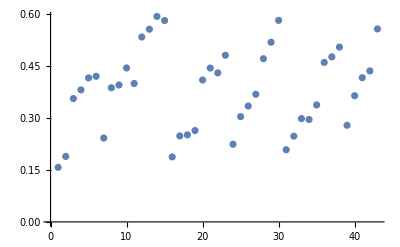

-Graphics-

```mathematica
l0={};
For[n=100,n<=200,n++,
l=SumTripleSpPoly[Prime[n]];
(*Print[l[[1]]];
Print[l[[2]]];*)
len=Length[l[[2]]];
s=0;
For[i=1,i<=len,i++,
If[l[[2]][[i]]==-4,s+=1/(l[[1]][[i]]l[[1]][[i+1]])];
];
AppendTo[l0,s//N];
];
ListPlot[l0]
```

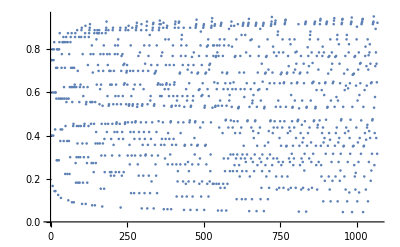

```mathematica
l0={};
For[n=10,n<=100,n++,
l=SumTripleSpPoly[Prime[n]];
(*Print[l[[1]]];
Print[l[[2]]];*)
len=Length[l[[2]]];
s=0;
For[i=1,i<=len,i++,
If[l[[2]][[i]]==-4&&((r=l[[1]][[i]]/l[[1]][[i+1]])<1),AppendTo[l0,r]];
];
];
ListPlot[l0]
```

```mathematica
l0
```

{0.1,1.16667,1.2,0.571429,3.33333,0.375,1.6,0.777778,4.5,0.222222,1.28571,0.625,2.66667,0.3,1.75,0.833333,0.857143,10.}

```mathematica
Prime[195]
```

1187

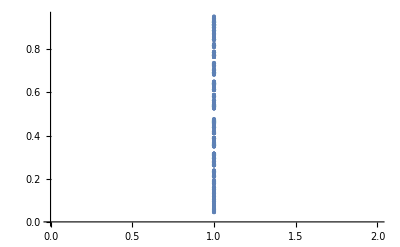

```mathematica
l0={};
For[n=35,n<=100,n++,
l=SumTripleSpPoly[Prime[n]];
(*Print[l[[1]]];
Print[l[[2]]];*)
len=Length[l[[2]]];
For[i=1,i<=len,i++,
If[l[[2]][[i]]==-4&&((r=l[[1]][[i]]/l[[1]][[i+1]])<1),AppendTo[l0,r]];
];
];
l1={};
For[i=1,i<=Length[l0],i++,
AppendTo[l1,{1,l0[[i]]}]
];
ListPlot[l1]
```

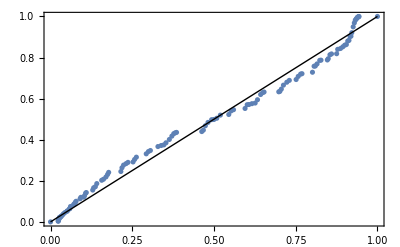

```mathematica
ProbabilityPlot[l0]
```

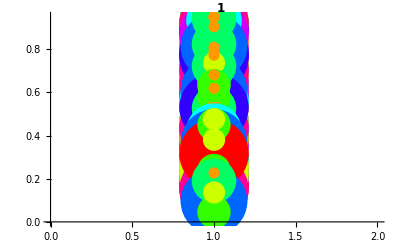

```mathematica
ListPlot[Labeled[Style[#1,PointSize[#2/50],Hue[#2/10]],Style[#2,Bold,12]]&@@@(Tally[l1])]
```

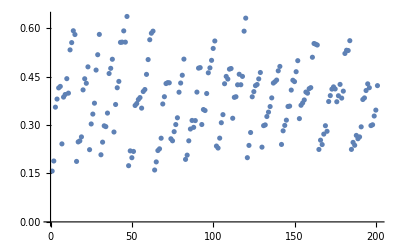

```mathematica
l0={};
For[n=100,n<=300,n++,
l=SumTriple[Prime[n]];
len=Length[l[[2]]];
s=0;
For[i=1,i<=len,i++,
If[l[[2]][[i]]==-4,s+=1/(l[[1]][[i]]l[[1]][[i+1]])];
];
AppendTo[l0,s//N];
];
ListPlot[l0]
```

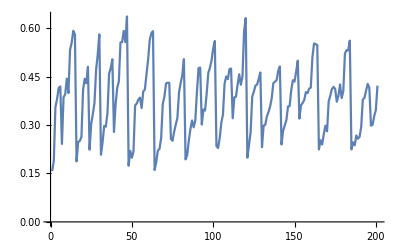

```mathematica
ListLinePlot[l0]
```

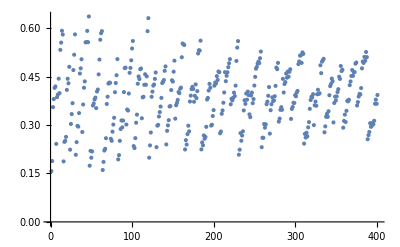

```mathematica
l0={};
For[n=100,n<=00,n++,
l=SumTriple[Prime[n]];
len=Length[l[[2]]];
s=0;
For[i=1,i<=len,i++,
If[l[[2]][[i]]==-4,s+=1/(l[[1]][[i]]l[[1]][[i+1]])];
];
AppendTo[l0,s//N];
];
ListPlot[l0]
```

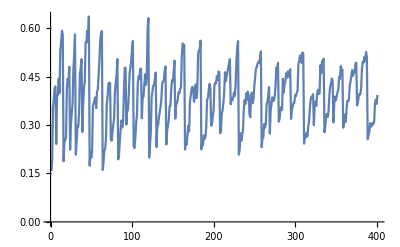

```mathematica
ListLinePlot[l0]
```

```mathematica
l
```

{{1,4,3,2,3,4,1},{0,-4,-4,0,0,-4}}

```mathematica
l0
```

{0.5}

```mathematica
SumTriple[n_Integer]:=
Module[{t,iterateMax,v,iterate,vw,vb,vn,x0,y0,a,b,ap,bp,k,Found,unclaimed,mpos,m,j,j1,res,m1,cpt=False,lF,v2count=0,v3count=0,v2value,v3value,FreeSides},
iterateMax=(GG0Index[n]-v3[n])/3;
v=Floor[Sqrt[n]];

v2value=v2[n];
v3value=v3[n];
FreeSides={};
lF=FareySequence[v];
vw=Denominator[lF];
vn=Numerator[lF];
vb=Table[-4,Length[vw]-1];


k=0;
Found=False;
For[iterate=1,iterate<=iterateMax&&!Found,iterate++,
For[j=1,j<Length[vw],j++,
a=vw[[j]];
b=vw[[j+1]];
If[vb[[j]]!=-4,Continue[]];
(* Check if even *)
If[v2count<v2value,
If[Mod[a^2+b^2,n]==0,vb=ReplacePart[vb,j->-2];v2count++;Continue[]]];
(* Check if odd *)
If[v3count<v3value,
If[Mod[a^2+a b+b^2,n]==0,vb=ReplacePart[vb,j->-3];v3count++;Continue[]]];

ap=vn[[j]];
bp=vn[[j+1]];
x0=n bp;y0=-n ap;
t=Ceiling[(x0-v)/b];
x0=x0-b t;
y0=y0 + a t;
If[y0<= v,vb=ReplacePart[vb,j->0]];
];

unclaimed=Flatten[Position[vb,-4]];
(* If no black vertices are labeled -4, then our computation is complete and safe *)

If[unclaimed=={},
Found=True;res=Max[vw];
Break[]
];

];
Return[{vw,vb}];
];
```

```mathematica
SumTriple[23]
```

{{1,4,3,2,3,4,1},{-4,-4,-4,-4,-4,-4}}

```mathematica
ZeroStartSpPoly[14]
```

{{1,4,7,3,2,3,7,4,1},{1,3,4,2,1,4,3,2}}

```mathematica
For[i=1,i<=20,i++,
q=Prime[i];
NN=2 q;
l=ZeroStartSpPoly[NN];
Print["q = ", q," and Max denom = ",Max[l[[1]]]," and max multiplier = ",l[[3]]];



];
```

q = 2 and Max denom = 2 and max multiplier = 4

q = 3 and Max denom = 3 and max multiplier = 12

q = 5 and Max denom = 5 and max multiplier = 30

q = 7 and Max denom = 7 and max multiplier = 56

q = 11 and Max denom = 11 and max multiplier = 132

q = 13 and Max denom = 13 and max multiplier = 208

q = 17 and Max denom = 17 and max multiplier = 306

q = 19 and Max denom = 19 and max multiplier = 456

q = 23 and Max denom = 23 and max multiplier = 552

q = 29 and Max denom = 29 and max multiplier = 986

q = 31 and Max denom = 31 and max multiplier = 992

q = 37 and Max denom = 37 and max multiplier = 1628

q = 41 and Max denom = 41 and max multiplier = 1968

q = 43 and Max denom = 43 and max multiplier = 2236

q = 47 and Max denom = 47 and max multiplier = 2632

q = 53 and Max denom = 53 and max multiplier = 2862

q = 59 and Max denom = 59 and max multiplier = 4130

q = 61 and Max denom = 61 and max multiplier = 4392

q = 67 and Max denom = 67 and max multiplier = 5494

q = 71 and Max denom = 71 and max multiplier = 5254